## Definations

```mathematica
Sx={{0,(√3)/2,0,0},{(√3)/2,0,1,0},{0,1,0,(√3)/2},{0,0,(√3)/2,0}};
Sy={{0,(√3)/(2ⅈ),0,0},{(√3)/(-2ⅈ),0,1/ⅈ,0},{0,-1/ⅈ,0,(√3)/(2ⅈ)},{0,0,(-√3)/(2ⅈ),0}};
Sz={{3/2,0,0,0},{0,1/2,0,0},{0,0,-1/2,0},{0,0,0,-3/2}};
Γx=Sx.Sx.Sx-41/20 Sx;
Γy=Sy.Sy.Sy-41/20 Sy;
Γz=Sz.Sz.Sz-41/20 Sz;
```

```mathematica
Sx//MatrixForm
Sy//MatrixForm
Sz//MatrixForm
Γx//MatrixForm
Γy//MatrixForm
Γz//MatrixForm
```

(0 | (√3)/2 | 0 | 0
(√3)/2 | 0 | 1 | 0
0 | 1 | 0 | (√3)/2
0 | 0 | (√3)/2 | 0)

(0 | -(ⅈ √3)/2 | 0 | 0
(ⅈ √3)/2 | 0 | -ⅈ | 0
0 | ⅈ | 0 | -(ⅈ √3)/2
0 | 0 | (ⅈ √3)/2 | 0)

(3/2 | 0 | 0 | 0
0 | 1/2 | 0 | 0
0 | 0 | -1/2 | 0
0 | 0 | 0 | -3/2)

(0 | -(3 √3)/20 | 0 | 3/4
-(3 √3)/20 | 0 | 9/20 | 0
0 | 9/20 | 0 | -(3 √3)/20
3/4 | 0 | -(3 √3)/20 | 0)

(0 | (3 ⅈ √3)/20 | 0 | (3 ⅈ)/4
-(3 ⅈ √3)/20 | 0 | -(9 ⅈ)/20 | 0
0 | (9 ⅈ)/20 | 0 | (3 ⅈ √3)/20
-(3 ⅈ)/4 | 0 | -(3 ⅈ √3)/20 | 0)

(3/10 | 0 | 0 | 0
0 | -9/10 | 0 | 0
0 | 0 | 9/10 | 0
0 | 0 | 0 | -3/10)

```mathematica
Tr[Sx.Sx]
Tr[Sx.Γx]
Tr[Γx.Γx]
Tr[Sx.Sy]
Tr[Γx.Γy]
Tr[Sx.Γy]
```

5

0

9/5

0

0

0

```mathematica
H[δ_,kx_,ky_,kz_]:=v (kx Sx+ky Sy+kz Sz)+v δ (kx Γx+ky Γy +kz Γz);
Simplify[H[δ,kx,ky,kz]]//MatrixForm
```

(3/10 kz v (5+δ) | -1/20 √3 (kx-ⅈ ky) v (-10+3 δ) | 0 | 3/4 (kx+ⅈ ky) v δ
-1/20 √3 (kx+ⅈ ky) v (-10+3 δ) | 1/10 kz v (5-9 δ) | 1/20 (kx-ⅈ ky) v (20+9 δ) | 0
0 | 1/20 (kx+ⅈ ky) v (20+9 δ) | 1/10 kz v (-5+9 δ) | -1/20 √3 (kx-ⅈ ky) v (-10+3 δ)
3/4 (kx-ⅈ ky) v δ | 0 | -1/20 √3 (kx+ⅈ ky) v (-10+3 δ) | -3/10 kz v (5+δ))

```mathematica
PropagatorS[ω_,kx_,ky_,kz_,δ_]:=Simplify[Inverse[-ⅈ ω IdentityMatrix[4]+H[δ,kx,ky,kz]]];
Factor[PropagatorS[ω,kx,ky,kz,0]]//MatrixForm
```

((2 (9 kx^2 kz v^3+9 ky^2 kz v^3+3 kz^3 v^3+14 ⅈ kx^2 v^2 ω+14 ⅈ ky^2 v^2 ω+2 ⅈ kz^2 v^2 ω+12 kz v ω^2+8 ⅈ ω^3))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | (2 √3 (kx-ⅈ ky) v (3 kx^2 v^2+3 ky^2 v^2-3 kz^2 v^2-8 ⅈ kz v ω+4 ω^2))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | -(4 √3 (kx-ⅈ ky)^2 v^2 (3 kz v+2 ⅈ ω))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | -(12 (kx-ⅈ ky)^3 v^3)/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2))
(2 √3 (kx+ⅈ ky) v (3 kx^2 v^2+3 ky^2 v^2-3 kz^2 v^2-8 ⅈ kz v ω+4 ω^2))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | (2 (3 kz v-2 ⅈ ω) (-3 kx^2 v^2-3 ky^2 v^2+3 kz^2 v^2+8 ⅈ kz v ω-4 ω^2))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | (4 (kx-ⅈ ky) v (3 kz v-2 ⅈ ω) (3 kz v+2 ⅈ ω))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | (4 √3 (kx-ⅈ ky)^2 v^2 (3 kz v-2 ⅈ ω))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2))
-(4 √3 (kx+ⅈ ky)^2 v^2 (3 kz v+2 ⅈ ω))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | (4 (kx+ⅈ ky) v (3 kz v-2 ⅈ ω) (3 kz v+2 ⅈ ω))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | -(2 (3 kz v+2 ⅈ ω) (-3 kx^2 v^2-3 ky^2 v^2+3 kz^2 v^2-8 ⅈ kz v ω-4 ω^2))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | (2 √3 (kx-ⅈ ky) v (3 kx^2 v^2+3 ky^2 v^2-3 kz^2 v^2+8 ⅈ kz v ω+4 ω^2))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2))
-(12 (kx+ⅈ ky)^3 v^3)/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | (4 √3 (kx+ⅈ ky)^2 v^2 (3 kz v-2 ⅈ ω))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | (2 √3 (kx+ⅈ ky) v (3 kx^2 v^2+3 ky^2 v^2-3 kz^2 v^2+8 ⅈ kz v ω+4 ω^2))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | -(2 (9 kx^2 kz v^3+9 ky^2 kz v^3+3 kz^3 v^3-14 ⅈ kx^2 v^2 ω-14 ⅈ ky^2 v^2 ω-2 ⅈ kz^2 v^2 ω+12 kz v ω^2-8 ⅈ ω^3))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)))

## Numerical Calculation

### self energy

```mathematica
RgV[δ_]:=Re[NIntegrate[Sin[θ]/(2π)^4 Cos[θ] 1/5(Tr[PropagatorS[ω,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ],δ].Sz]+Tr[PropagatorS[-ω,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ],δ].Sz])/.v->1,{ω,-Infinity,Infinity},{ϕ,0,2π},{θ,0,π}]]
RgDV[δ_]:=Re[NIntegrate[Sin[θ]/(2π)^4 Cos[θ] 5/9(Tr[PropagatorS[ω,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ],δ].Γz]+Tr[PropagatorS[-ω,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ],δ].Γz])/.v->1,{ω,-Infinity,Infinity},{ϕ,0,2π},{θ,0,π}]]
```

```mathematica
BetaD[δ_]:=RgDV[δ]-δ RgV[δ]
```

{-0.095,2.75248×10^-6}

{-0.094,2.32157×10^-6}

{-0.093,1.89809×10^-6}

{-0.092,1.4822×10^-6}

{-0.091,1.07385×10^-6}

{-0.09,6.73053×10^-7}

{-0.089,2.79995×10^-7}

{-0.088,-1.05457×10^-7}

{-0.087,-4.83233×10^-7}

{-0.086,-8.51132×10^-7}

{{-0.095,2.75248×10^-6},{-0.094,2.32157×10^-6},{-0.093,1.89809×10^-6},{-0.092,1.4822×10^-6},{-0.091,1.07385×10^-6},{-0.09,6.73053×10^-7},{-0.089,2.79995×10^-7},{-0.088,-1.05457×10^-7},{-0.087,-4.83233×10^-7},{-0.086,-8.51132×10^-7}}

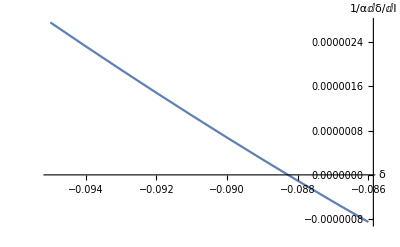

```mathematica
data1={};
For[i=0,i<10,i++,y=BetaD[-0.095+0.001i];data1=AppendTo[data1,{-0.095+0.001i,y}];Print[{-0.095+0.001i,y}]]
data1
ListLinePlot[data1,AxesLabel->{"δ","1/αⅆδ/ⅆl"}]
```

{-0.13,0.0000222943}

{-0.12,0.0000158624}

{-0.11,0.0000100925}

{-0.1,5.01834×10^-6}

{-0.09,6.73053×10^-7}

{-0.08,-2.90921×10^-6}

{-0.07,-5.69477×10^-6}

{-0.06,-7.64862×10^-6}

{-0.05,-8.73966×10^-6}

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000549153-3.54976×10^-22 ⅈ and 6.90641×10^-10 for the integral and error estimates.

{-0.04,-8.93024×10^-6}

{-0.03,-8.18671×10^-6}

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000276644-2.82438×10^-22 ⅈ and 6.74735×10^-10 for the integral and error estimates.

{-0.02,-6.47398×10^-6}

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000138849-1.3569×10^-21 ⅈ and 4.98774×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{-0.01,-3.75693×10^-6}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0.,-1.77246×10^-17}

{0.01,4.83254×10^-6}

{0.02,0.0000107768}

{0.03,0.0000178693}

{0.04,0.0000261467}

{0.05,0.0000356464}

{0.06,0.0000464057}

{{-0.13,0.0000222943},{-0.12,0.0000158624},{-0.11,0.0000100925},{-0.1,5.01834×10^-6},{-0.09,6.73053×10^-7},{-0.08,-2.90921×10^-6},{-0.07,-5.69477×10^-6},{-0.06,-7.64862×10^-6},{-0.05,-8.73966×10^-6},{-0.04,-8.93024×10^-6},{-0.03,-8.18671×10^-6},{-0.02,-6.47398×10^-6},{-0.01,-3.75693×10^-6},{0.,-1.77246×10^-17},{0.01,4.83254×10^-6},{0.02,0.0000107768},{0.03,0.0000178693},{0.04,0.0000261467},{0.05,0.0000356464},{0.06,0.0000464057}}

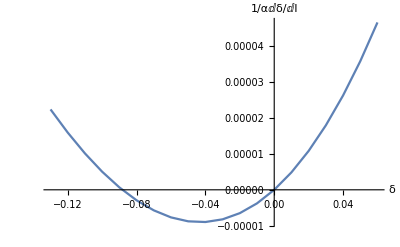

```mathematica
data2={};
For[i=0,i<20,i++,y=BetaD[-0.13+0.01i];data2=AppendTo[data2,{-0.13+0.01i,y}];Print[{-0.13+0.01i,y}]]
data2
ListLinePlot[data2,AxesLabel->{"δ","1/αⅆδ/ⅆl"}]
```

### band structure

```mathematica
Eigenvalues[H[-0.085,kx,ky,kz]/.v->1]
```

{1. Root[1. kx^4-(0.+1.15235×10^-16 ⅈ) kx^3 ky+(0.929204+0. ⅈ) kx^2 ky^2+(0.+1.15235×10^-16 ⅈ) kx ky^3+(1.+0. ⅈ) ky^4+0.929204 kx^2 kz^2+(0.929204+0. ⅈ) ky^2 kz^2+1. kz^4+(-9.21878×10^-16 kx^2 kz-(9.21878×10^-16+0. ⅈ) ky^2 kz-3.07293×10^-16 kz^3) #1+(-3.46881 kx^2-(3.46881+0. ⅈ) ky^2-3.46881 kz^2) #1^2+1.38392 #1^4&,1],1. Root[1. kx^4-(0.+1.15235×10^-16 ⅈ) kx^3 ky+(0.929204+0. ⅈ) kx^2 ky^2+(0.+1.15235×10^-16 ⅈ) kx ky^3+(1.+0. ⅈ) ky^4+0.929204 kx^2 kz^2+(0.929204+0. ⅈ) ky^2 kz^2+1. kz^4+(-9.21878×10^-16 kx^2 kz-(9.21878×10^-16+0. ⅈ) ky^2 kz-3.07293×10^-16 kz^3) #1+(-3.46881 kx^2-(3.46881+0. ⅈ) ky^2-3.46881 kz^2) #1^2+1.38392 #1^4&,2],1. Root[1. kx^4-(0.+1.15235×10^-16 ⅈ) kx^3 ky+(0.929204+0. ⅈ) kx^2 ky^2+(0.+1.15235×10^-16 ⅈ) kx ky^3+(1.+0. ⅈ) ky^4+0.929204 kx^2 kz^2+(0.929204+0. ⅈ) ky^2 kz^2+1. kz^4+(-9.21878×10^-16 kx^2 kz-(9.21878×10^-16+0. ⅈ) ky^2 kz-3.07293×10^-16 kz^3) #1+(-3.46881 kx^2-(3.46881+0. ⅈ) ky^2-3.46881 kz^2) #1^2+1.38392 #1^4&,3],1. Root[1. kx^4-(0.+1.15235×10^-16 ⅈ) kx^3 ky+(0.929204+0. ⅈ) kx^2 ky^2+(0.+1.15235×10^-16 ⅈ) kx ky^3+(1.+0. ⅈ) ky^4+0.929204 kx^2 kz^2+(0.929204+0. ⅈ) ky^2 kz^2+1. kz^4+(-9.21878×10^-16 kx^2 kz-(9.21878×10^-16+0. ⅈ) ky^2 kz-3.07293×10^-16 kz^3) #1+(-3.46881 kx^2-(3.46881+0. ⅈ) ky^2-3.46881 kz^2) #1^2+1.38392 #1^4&,4]}

```mathematica
Plot3D[{1. Root[1. kx^4-(0.+1.1523471078369186*^-16 ⅈ) kx^3 ky+(0.9292038956801795+0. ⅈ) kx^2 ky^2+(0.+1.1523471078369186*^-16 ⅈ) kx ky^3+(1.+0. ⅈ) ky^4+0.9292038956801788 kx^2 kz^2+(0.9292038956801788+0. ⅈ) ky^2 kz^2+0.9999999999999999 kz^4+(-9.218776862695349*^-16 kx^2 kz-(9.218776862695349*^-16+0. ⅈ) ky^2 kz-3.0729256208984493*^-16 kz^3) #1+(-3.468805627453337 kx^2-(3.468805627453337+0. ⅈ) ky^2-3.4688056274533356 kz^2) #1^2+1.3839226681215504 #1^4&,1],1. Root[1. kx^4-(0.+1.1523471078369186*^-16 ⅈ) kx^3 ky+(0.9292038956801795+0. ⅈ) kx^2 ky^2+(0.+1.1523471078369186*^-16 ⅈ) kx ky^3+(1.+0. ⅈ) ky^4+0.9292038956801788 kx^2 kz^2+(0.9292038956801788+0. ⅈ) ky^2 kz^2+0.9999999999999999 kz^4+(-9.218776862695349*^-16 kx^2 kz-(9.218776862695349*^-16+0. ⅈ) ky^2 kz-3.0729256208984493*^-16 kz^3) #1+(-3.468805627453337 kx^2-(3.468805627453337+0. ⅈ) ky^2-3.4688056274533356 kz^2) #1^2+1.3839226681215504 #1^4&,2],1. Root[1. kx^4-(0.+1.1523471078369186*^-16 ⅈ) kx^3 ky+(0.9292038956801795+0. ⅈ) kx^2 ky^2+(0.+1.1523471078369186*^-16 ⅈ) kx ky^3+(1.+0. ⅈ) ky^4+0.9292038956801788 kx^2 kz^2+(0.9292038956801788+0. ⅈ) ky^2 kz^2+0.9999999999999999 kz^4+(-9.218776862695349*^-16 kx^2 kz-(9.218776862695349*^-16+0. ⅈ) ky^2 kz-3.0729256208984493*^-16 kz^3) #1+(-3.468805627453337 kx^2-(3.468805627453337+0. ⅈ) ky^2-3.4688056274533356 kz^2) #1^2+1.3839226681215504 #1^4&,3],1. Root[1. kx^4-(0.+1.1523471078369186*^-16 ⅈ) kx^3 ky+(0.9292038956801795+0. ⅈ) kx^2 ky^2+(0.+1.1523471078369186*^-16 ⅈ) kx ky^3+(1.+0. ⅈ) ky^4+0.9292038956801788 kx^2 kz^2+(0.9292038956801788+0. ⅈ) ky^2 kz^2+0.9999999999999999 kz^4+(-9.218776862695349*^-16 kx^2 kz-(9.218776862695349*^-16+0. ⅈ) ky^2 kz-3.0729256208984493*^-16 kz^3) #1+(-3.468805627453337 kx^2-(3.468805627453337+0. ⅈ) ky^2-3.4688056274533356 kz^2) #1^2+1.3839226681215504 #1^4&,4]}/.{kz->0},{kx,-5,5},{ky,-5,5}]
```

-Graphics3D-

### polarization

```mathematica
BetaG[δ_]:=Re[NIntegrate[Sin[θ]/(2π)^4 Simplify[D[Tr[PropagatorS[ω,Sin[θ]Cos[ϕ]+q,Sin[θ]Sin[ϕ],Cos[θ],δ].PropagatorS[ω,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ],δ]],{q,2}]/.q->0]/.v->1,{ω,-Infinity,Infinity},{θ,0,π},{ϕ,0,2π}]];
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.468246+7.1621×10^-18 ⅈ and 0.0000679399 for the integral and error estimates.

{-1.,-0.468246}

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.1436-6.65942×10^-18 ⅈ and 0.000523393 for the integral and error estimates.

{-0.9,-1.1436}

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.26942-4.19441×10^-15 ⅈ and 0.00130747 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{-0.8,-2.26942}

{-0.7,-0.582015}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{-0.6,-0.341967}

{-0.5,-0.246883}

{-0.4,-0.196814}

{-0.3,-0.167048}

{-0.2,-0.148808}

{-0.1,-0.138543}

{0.,-0.135095}

{0.1,-0.13905}

{0.2,-0.153475}

{0.3,-0.187659}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0.4,-0.276214}

{0.5,-0.705617}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{0.6,-0.832222}

{0.7,-0.248861}

{0.8,-0.143596}

{0.9,-0.0999112}

{1.,-0.0761781}

{{-1.,-0.468246},{-0.9,-1.1436},{-0.8,-2.26942},{-0.7,-0.582015},{-0.6,-0.341967},{-0.5,-0.246883},{-0.4,-0.196814},{-0.3,-0.167048},{-0.2,-0.148808},{-0.1,-0.138543},{0.,-0.135095},{0.1,-0.13905},{0.2,-0.153475},{0.3,-0.187659},{0.4,-0.276214},{0.5,-0.705617},{0.6,-0.832222},{0.7,-0.248861},{0.8,-0.143596},{0.9,-0.0999112},{1.,-0.0761781}}

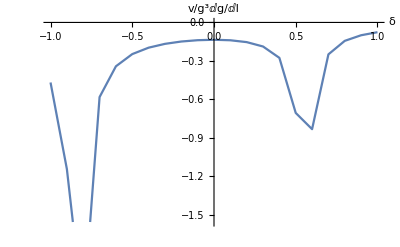

485.135

```mathematica
t0=AbsoluteTime[];
data3={};
For[i=0,i<21,i++,y=BetaG[-1+0.1i];data3=AppendTo[data3,{-1+0.1i,y}];Print[{-1+0.1i,y}]]
data3
ListLinePlot[data3,AxesLabel->{"δ","v/g^3ⅆg/ⅆl"},AxesOrigin->{0,0}]
N[(AbsoluteTime[]-t0)/60]
```

```mathematica
BetaG[0.55]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -6.78431-2.75184×10^-7 ⅈ and 0.00189293 for the integral and error estimates.

-6.78431

```mathematica
BetaG[-0.85]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.5205+3.1998×10^-15 ⅈ and 0.00344221 for the integral and error estimates.

-4.5205

```mathematica
Ma={-0.95,-0.75,0.45,0.65};
ParallelTable[BetaG[Ma[[i]]],{i,4}]//MatrixForm
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.661165-9.53489×10^-18 ⅈ and 0.000165266 for the integral and error estimates.

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.387958+3.64439×10^-19 ⅈ and 0.0000179156 for the integral and error estimates.

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.385832+4.99186×10^-19 ⅈ and 0.0000200576 for the integral and error estimates.

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.919177+2.03314×10^-18 ⅈ and 0.000423285 for the integral and error estimates.

(-0.661165
-0.919177
-0.387958
-0.385832)

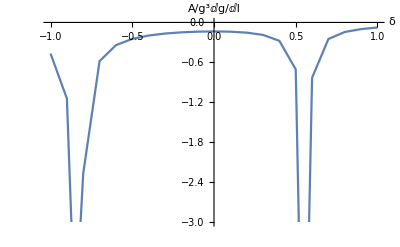

```mathematica
ListLinePlot[{{-1.,-0.4682460138621485},{-0.9,-1.1435964586254488},{-0.85,-4.5205},{-0.8,-2.269416897212586},{-0.7,-0.5820149540475219},{-0.6,-0.34196710293447363},{-0.5,-0.2468826312102792},{-0.3999999999999999,-0.1968140376375199},{-0.29999999999999993,-0.1670480237213522},{-0.19999999999999996,-0.1488077563762979},{-0.09999999999999998,-0.1385433777964312},{0.,-0.13509491166529428},{0.10000000000000009,-0.13905013623905146},{0.20000000000000018,-0.1534749439911696},{0.30000000000000004,-0.18765876607519202},{0.40000000000000013,-0.27621356547740417},{0.5,-0.7056166233835922},{0.55,-6.78431},{0.6000000000000001,-0.8322223111116918},{0.7000000000000002,-0.24886060558019668},{0.8,-0.14359605347752646},{0.9000000000000001,-0.09991117586574913},{1.,-0.0761780580658049}},AxesLabel->{"δ","A/g^3ⅆg/ⅆl"},AxesOrigin->{0,0},InterpolationOrder->1,PlotRange->{{-1,1},{-3,0}}]
```

### topological phase transition

```mathematica
BetaD[0]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.77246×10^-17+0. ⅈ and 7.81978×10^-14 for the integral and error estimates.

-1.77246×10^-17

{-1.,-0.000434766}

{-0.95,-0.000353772}

{-0.9,-0.000234855}

{-0.85,-0.0000682185}

{-0.8,0.000129563}

{-0.75,0.000276372}

{-0.7,0.00037416}

{-0.65,0.000430946}

{-0.6,0.000453847}

{-0.55,0.00044924}

{-0.5,0.000422909}

{-0.45,0.00038015}

{-0.4,0.000325879}

{-0.35,0.000264716}

{-0.3,0.000201053}

{-0.25,0.00013913}

{-0.2,0.0000830844}

{-0.15,0.0000370127}

{-0.1,5.01834×10^-6}

{-0.05,-8.73966×10^-6}

{0.,-1.77246×10^-17}

{0.05,0.0000356464}

{0.1,0.000102802}

{0.15,0.000206308}

{0.2,0.000351291}

{0.25,0.000543212}

{0.3,0.000787915}

{0.35,0.00109168}

{0.4,0.0014613}

{0.45,0.00190409}

{0.5,0.00242803}

{0.55,0.00304177}

{0.6,0.00364471}

{0.65,0.00410157}

{0.7,0.00444672}

{0.75,0.00470579}

{0.8,0.0048974}

{0.85,0.00503539}

{0.9,0.00513021}

{0.95,0.00518989}

{1.,0.0052207}

{{-1.,-0.000434766},{-0.95,-0.000353772},{-0.9,-0.000234855},{-0.85,-0.0000682185},{-0.8,0.000129563},{-0.75,0.000276372},{-0.7,0.00037416},{-0.65,0.000430946},{-0.6,0.000453847},{-0.55,0.00044924},{-0.5,0.000422909},{-0.45,0.00038015},{-0.4,0.000325879},{-0.35,0.000264716},{-0.3,0.000201053},{-0.25,0.00013913},{-0.2,0.0000830844},{-0.15,0.0000370127},{-0.1,5.01834×10^-6},{-0.05,-8.73966×10^-6},{0.,-1.77246×10^-17},{0.05,0.0000356464},{0.1,0.000102802},{0.15,0.000206308},{0.2,0.000351291},{0.25,0.000543212},{0.3,0.000787915},{0.35,0.00109168},{0.4,0.0014613},{0.45,0.00190409},{0.5,0.00242803},{0.55,0.00304177},{0.6,0.00364471},{0.65,0.00410157},{0.7,0.00444672},{0.75,0.00470579},{0.8,0.0048974},{0.85,0.00503539},{0.9,0.00513021},{0.95,0.00518989},{1.,0.0052207}}

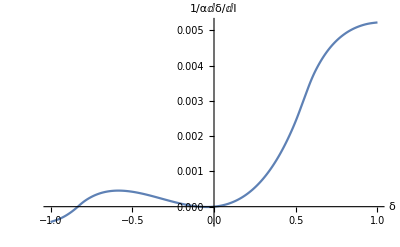

```mathematica
data4={};
For[i=0,i<41,i++,y=BetaD[-1+0.05i];data4=AppendTo[data4,{-1+0.05i,y}];Print[{-1+0.05i,y}]]
data4
ListLinePlot[data4,AxesLabel->{"δ","1/αⅆδ/ⅆl"},InterpolationOrder->2]
```

{-0.85,-0.0000682185}

{-0.845,-0.0000484775}

{-0.84,-0.0000281216}

{-0.835,-7.13621×10^-6}

{-0.83,0.000014202}

{-0.825,0.0000349713}

{-0.82,0.0000551097}

{-0.815,0.0000746287}

{-0.81,0.0000935371}

{-0.805,0.000111845}

{-0.8,0.000129563}

{{-0.85,-0.0000682185},{-0.845,-0.0000484775},{-0.84,-0.0000281216},{-0.835,-7.13621×10^-6},{-0.83,0.000014202},{-0.825,0.0000349713},{-0.82,0.0000551097},{-0.815,0.0000746287},{-0.81,0.0000935371},{-0.805,0.000111845},{-0.8,0.000129563}}

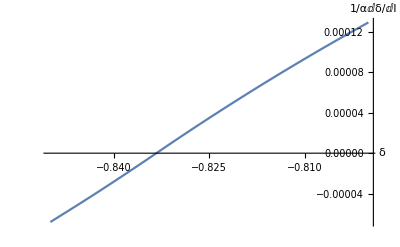

```mathematica
data5={};
For[i=0,i<11,i++,y=BetaD[-0.85+0.005i];data5=AppendTo[data5,{-0.85+0.005i,y}];Print[{-0.85+0.005i,y}]]
data5
ListLinePlot[data5,InterpolationOrder->2,AxesLabel->{"δ","1/αⅆδ/ⅆl"}]
```

{-0.975,-0.000464175}

{-0.925,-0.000504759}

{-0.875,-0.000520221}

{-0.825,-0.000509868}

{-0.775,-0.000473613}

{-0.725,-0.000412355}

{-0.675,-0.000328765}

{-0.625,-0.000228478}

{-0.575,-0.000122217}

{-0.525,-0.000029537}

{-0.475,0.0000144414}

{-0.425,-0.0000537437}

{-0.375,-0.000351058}

{-0.325,-0.00110056}

{-0.275,-0.00274984}

{-0.225,-0.00626564}

{-0.175,-0.0130545}

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000276103+1.17155×10^-21 ⅈ and 5.05523×10^-10 for the integral and error estimates.

{-0.125,-0.0214486}

{-0.075,-0.0363438}

{-0.025,-0.102732}

{0.025,-0.091582}

{0.075,-0.0258227}

{0.125,-0.0123089}

{0.175,-0.00636273}

{0.225,-0.00299131}

{0.275,-0.000818454}

{0.325,0.000692553}

{0.375,0.00179597}

{0.425,0.00262834}

{0.475,0.00326976}

{0.525,0.00377041}

{0.575,0.00416347}

{0.625,0.00447179}

{0.675,0.00471171}

{0.725,0.00489532}

{0.775,0.00503174}

{0.825,0.00512805}

{0.875,0.00518983}

{0.925,0.00522158}

{0.975,0.00522695}

{{-0.975,-0.000464175},{-0.925,-0.000504759},{-0.875,-0.000520221},{-0.825,-0.000509868},{-0.775,-0.000473613},{-0.725,-0.000412355},{-0.675,-0.000328765},{-0.625,-0.000228478},{-0.575,-0.000122217},{-0.525,-0.000029537},{-0.475,0.0000144414},{-0.425,-0.0000537437},{-0.375,-0.000351058},{-0.325,-0.00110056},{-0.275,-0.00274984},{-0.225,-0.00626564},{-0.175,-0.0130545},{-0.125,-0.0214486},{-0.075,-0.0363438},{-0.025,-0.102732},{0.025,-0.091582},{0.075,-0.0258227},{0.125,-0.0123089},{0.175,-0.00636273},{0.225,-0.00299131},{0.275,-0.000818454},{0.325,0.000692553},{0.375,0.00179597},{0.425,0.00262834},{0.475,0.00326976},{0.525,0.00377041},{0.575,0.00416347},{0.625,0.00447179},{0.675,0.00471171},{0.725,0.00489532},{0.775,0.00503174},{0.825,0.00512805},{0.875,0.00518983},{0.925,0.00522158},{0.975,0.00522695}}

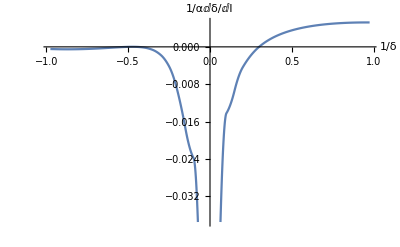

```mathematica
data6={};
For[i=0,i<40,i++,y=BetaD[1/(-0.975+0.05i)];data6=AppendTo[data6,{-0.975+0.05i,y}];Print[{-0.975+0.05i,y}]]
data6
ListLinePlot[data6,AxesLabel->{"1/δ","1/αⅆδ/ⅆl"},InterpolationOrder->2]
```

## Numerical Calculation for A<0

```mathematica
RgV2[δ_]:=Re[NIntegrate[Sin[θ]/(2π)^4 Cos[θ] 1/5(Tr[PropagatorS[ω,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ],δ].Sz]+Tr[PropagatorS[-ω,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ],δ].Sz])/.v->-1,{ω,-Infinity,Infinity},{ϕ,0,2π},{θ,0,π}]];
RgDV2[δ_]:=Re[NIntegrate[Sin[θ]/(2π)^4 Cos[θ] 5/9(Tr[PropagatorS[ω,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ],δ].Γz]+Tr[PropagatorS[-ω,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ],δ].Γz])/.v->-1,{ω,-Infinity,Infinity},{ϕ,0,2π},{θ,0,π}]];
```

```mathematica
BetaD2[δ_]:=RgDV2[δ]-δ RgV2[δ];
```

{-1.,0.000434766}

{-0.95,0.000353772}

{-0.9,0.000234855}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{-0.85,0.0000682185}

{-0.8,-0.000129563}

{-0.75,-0.000276372}

{-0.7,-0.00037416}

{-0.65,-0.000430946}

{-0.6,-0.000453847}

{-0.55,-0.00044924}

{-0.5,-0.000422909}

{-0.45,-0.00038015}

{-0.4,-0.000325879}

{-0.35,-0.000264716}

{-0.3,-0.000201053}

{-0.25,-0.00013913}

{-0.2,-0.0000830844}

{-0.15,-0.0000370127}

{-0.1,-5.01834×10^-6}

{-0.05,8.73966×10^-6}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.75421×10^-17+0. ⅈ and 7.81972×10^-14 for the integral and error estimates.

{0.,1.75421×10^-17}

{0.05,-0.0000356464}

{0.1,-0.000102802}

{0.15,-0.000206308}

{0.2,-0.000351291}

{0.25,-0.000543212}

{0.3,-0.000787915}

{0.35,-0.00109168}

{0.4,-0.0014613}

{0.45,-0.00190409}

{0.5,-0.00242803}

{0.55,-0.00304177}

{0.6,-0.00364471}

{0.65,-0.00410157}

{0.7,-0.00444672}

{0.75,-0.00470579}

{0.8,-0.0048974}

{0.85,-0.00503539}

{0.9,-0.00513021}

{0.95,-0.00518989}

{1.,-0.0052207}

{{-1.,0.000434766},{-0.95,0.000353772},{-0.9,0.000234855},{-0.85,0.0000682185},{-0.8,-0.000129563},{-0.75,-0.000276372},{-0.7,-0.00037416},{-0.65,-0.000430946},{-0.6,-0.000453847},{-0.55,-0.00044924},{-0.5,-0.000422909},{-0.45,-0.00038015},{-0.4,-0.000325879},{-0.35,-0.000264716},{-0.3,-0.000201053},{-0.25,-0.00013913},{-0.2,-0.0000830844},{-0.15,-0.0000370127},{-0.1,-5.01834×10^-6},{-0.05,8.73966×10^-6},{0.,1.75421×10^-17},{0.05,-0.0000356464},{0.1,-0.000102802},{0.15,-0.000206308},{0.2,-0.000351291},{0.25,-0.000543212},{0.3,-0.000787915},{0.35,-0.00109168},{0.4,-0.0014613},{0.45,-0.00190409},{0.5,-0.00242803},{0.55,-0.00304177},{0.6,-0.00364471},{0.65,-0.00410157},{0.7,-0.00444672},{0.75,-0.00470579},{0.8,-0.0048974},{0.85,-0.00503539},{0.9,-0.00513021},{0.95,-0.00518989},{1.,-0.0052207}}

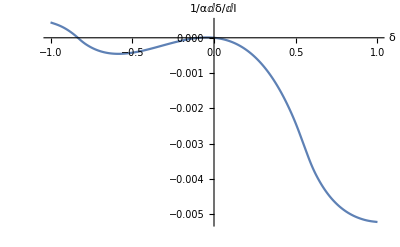

```mathematica
data7={};
For[i=0,i<41,i++,y=BetaD2[-1+0.05i];data7=AppendTo[data7,{-1+0.05i,y}];Print[{-1+0.05i,y}]]
data7
ListLinePlot[data7,AxesLabel->{"δ","1/αⅆδ/ⅆl"},InterpolationOrder->2]
```